```mathematica
SetDirectory[NotebookDirectory[]]
FileNames[]// TableForm;
RawPol=Import["Polaire.csv"];

{DV,DA}=Dimensions[RawPol];
{MinW,MaxW,MinA,MaxA}={RawPol[[2, 1]], RawPol[[DV, 1]], RawPol[[1, 2]], RawPol[[1, DA]]};{Minr,Maxr}={1,7};RawPolaire=Table[{{RawPol[[j,1]],RawPol[[1,i]]},RawPol[[j,i]]},{j,2,DV},{i,2,DA}] ;
Voilier=Interpolation[Flatten[RawPolaire,1]];
Yacht[W_,A_]:=If[A≥MinA,Voilier[W,A],0]
```

```mathematica
"/Users/mhk/Documents/ZHAW/ba/Mathematica Source
```

```mathematica
Voilier[5.23,124.2]
```

2.87871

```mathematica
Print[{MinW,MaxW,MinA,MaxA}]
```

{1,20,35,180}

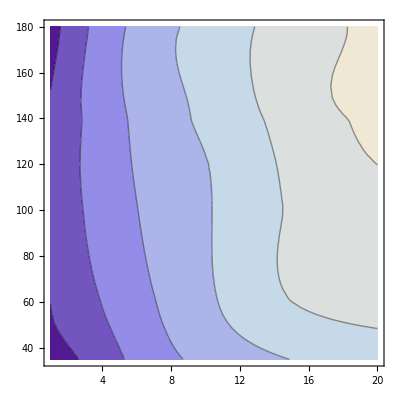

```mathematica
ContourPlot[Voilier[w,a],{w,MinW,MaxW},{a,MinA,MaxA}]

DiagrammePolaire:=Module[{PolarDiagram,Vents,PolarFrameR,PolarFrameA,WStepsA,WStepsB,Allures},PolarDiagram=Table[Graphics[ParametricPlot[Voilier[w,a]{Cos[π/2(1-a/90)],Sin[π/2(1-a/90)]},{a,MinA,MaxA},PlotStyle -> {RGBColor[(w-MinW)/(MaxW-MinW),0,1-(w-MinW)/(MaxW-MinW)],Thickness[0.00.5]}]],{w,MinW,MaxW}];
Vents=Graphics[Table[Text[w,Voilier[w,MinA]{ Cos[π/2(1-MinA/90)], Sin[π/2(1-MinA/90)]},{1,1}],{w,MinW,MaxW,5}]];
PolarFrameR=Graphics[Table[{RGBColor[0.3,0,1],Line[{Minr {Cos[π/2(1-a/90)], Sin[π/2(1-a/90)]},Maxr {Cos[π/2(1-a/90)],Sin[π/2(1-a/90)]}} ]},{a,0,180,10}]];
PolarFrameA=Table[ParametricPlot[r{ Cos[π/2(1-a/90)], Sin[π/2(1-a/90)]},{a,0,180}],{r,Minr,Maxr}];
WStepsA=Graphics[Table[Text[i,{-0.5,i}],{i,Minr,Maxr}]];
WStepsB=Graphics[Table[Text[i,{-0.5,-i}],{i,Minr,Maxr}]];
Allures=Graphics[Table[Text[a,(Maxr+0.5){ Cos[π/2(1-a/90)], Sin[π/2(1-a/90)]}],{a,30,150,30}]];
Show[PolarFrameR,WStepsA,WStepsB,Allures,Vents,PolarFrameA,PolarDiagram,PlotLabel-> "Diagramme Polaire M. Stoll",Frame-> True,FrameTicks-> None]]
```

```mathematica
Allure =180/Pi N[ArcCos[(r.wa)/(R Wa)]]
```

(180 ArcCos[(r.wa)/(R Wa)])/π

```mathematica
Vitesse= Yacht[Wa,Allure]
```

If[(180 ArcCos[(r.wa)/(R Wa)])/π≥35,Voilier[Wa,(180 ArcCos[(r.wa)/(R Wa)])/π],0]

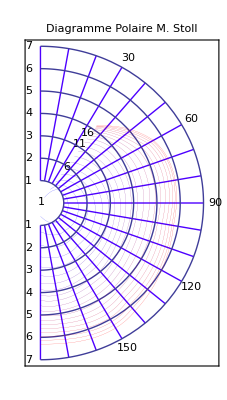

```mathematica
DiagrammePolaire
```